```mathematica
SetDirectory["/Users/gravel/projects/taino/frequencies/results/2013-03-14"]
a=Import["trimmed_outall.freqs.gz","TSV"];
```

/Users/gravel/projects/taino/frequencies/results/2013-03-14

```mathematica
Length[a]
```

94524

```mathematica
a=Select[a,Not[MemberQ[Flatten[#],"-"]]&];
Length[a]
```

29354

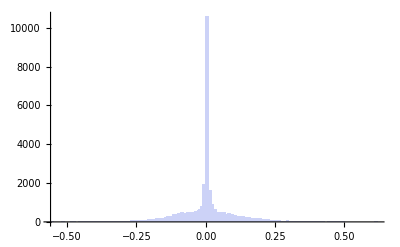

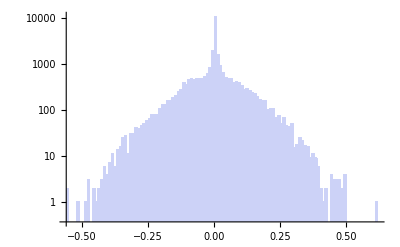

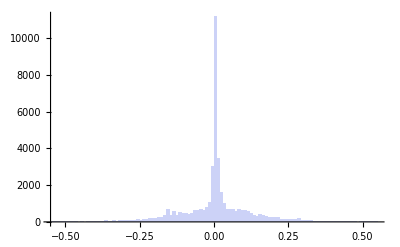

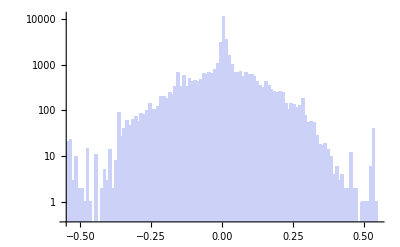

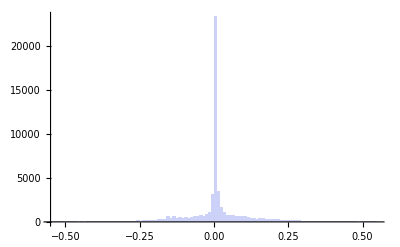

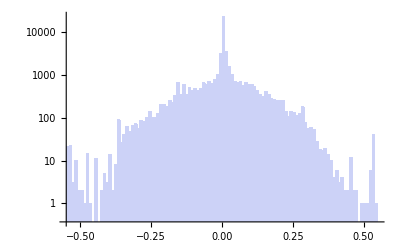

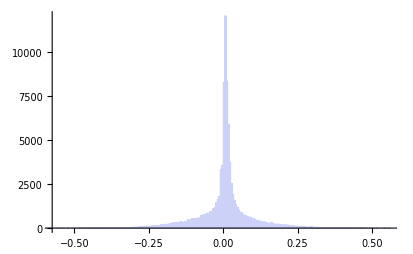

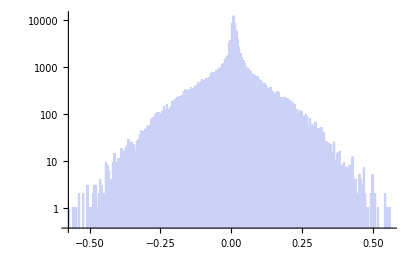

```mathematica
Histogram[a[[2;;,4]]- a[[2;;,7]]]
Histogram[a[[2;;,4]]- a[[2;;,7]],Automatic,"LogCount"]
```

```mathematica
a[[1]]
```

{chrom,pos,CLM_lo,CLM,CLM_hi,MXL_lo,MXL,MXL_hi,PUR_lo,PUR,PUR_hi}

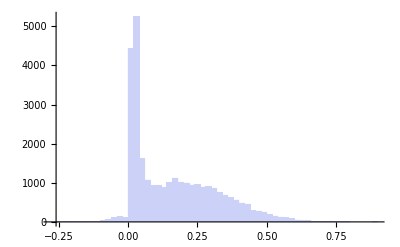

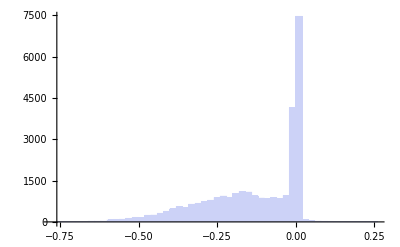

```mathematica
(*Look for nonoverlaps in CLM vs MXL*)
Histogram[a[[2;;,5]]- a[[2;;,6]]]
Histogram[a[[2;;,3]]- a[[2;;,8]]]
```

```mathematica
a[[1]]
```

{Chr,Pos,CLM_low,CLM_est,CLM_high,MXL_low,MXL_est,MXL_high,PUR_low,PUR_est,PUR_high}

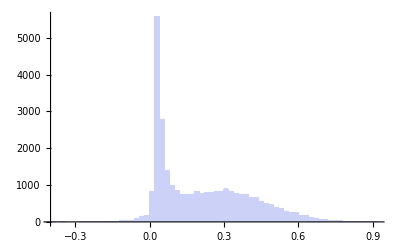

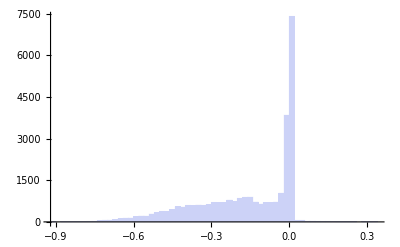

```mathematica
Histogram[a[[2;;,11]]- a[[2;;,6]]]
Histogram[a[[2;;,9]]- a[[2;;,8]]]
```

```mathematica
columns=a[[1]]
```

{chrom,pos,CLM_lo,CLM,CLM_hi,MXL_lo,MXL,MXL_hi,PUR_lo,PUR,PUR_hi}

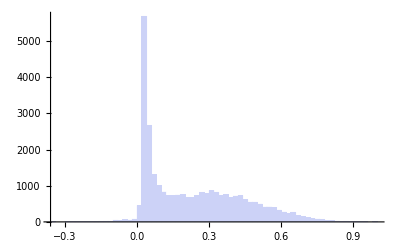

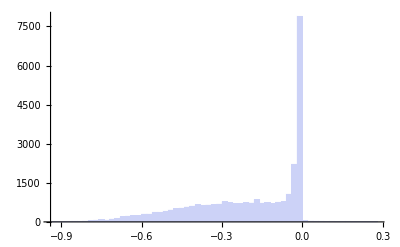

```mathematica
Histogram[a[[2;;,11]]- a[[2;;,3]]]
Histogram[a[[2;;,9]]- a[[2;;,5]]]
```

```mathematica
columns
```

columns

```mathematica
startpos=1

ci2sig=(2*1.96)
σCLM=(a[[startpos;;,5]]-a[[startpos;;,3]])/ci2sig;
xCLM=a[[startpos;;,4]];
σMXL=(a[[startpos;;,8]]-a[[startpos;;,6]])/ci2sig;
xMXL=a[[startpos;;,7]];
σPUR=(a[[startpos;;,11]]-a[[startpos;;,9]])/ci2sig;
xPUR=a[[startpos;;,10]];
markerPos=Table[i,{i,1,Length[a]-startpos+1}];
chr=a[[startpos;;,1]];
pos=a[[startpos;;,2]];
colorcode=Map[If[OddQ[#],LightBlue,Blue]&,chr];
```

1

3.92

```mathematica
selectPUR=(Map[(#≠"NA" && #>0.2&& #<.8) &,xPUR]);
selectCLM=(Map[(#≠"NA" && #>0.2&& #<.8)&,xCLM]);
selectMXL=(Map[(#≠"NA" && #>0.2&& #<.8)&,xMXL]);
```

```mathematica
4*Pick[σCLM,selectPUR][[1;;10]]
```

{0.132653,0.397959,0.438776,0.479592,0.459184,0.193878,0.326531,0.44898,0.316327,0.346939}

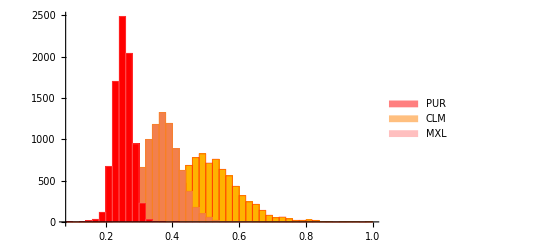

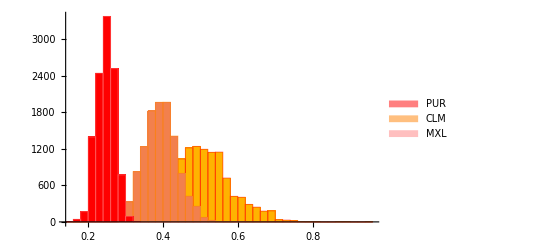

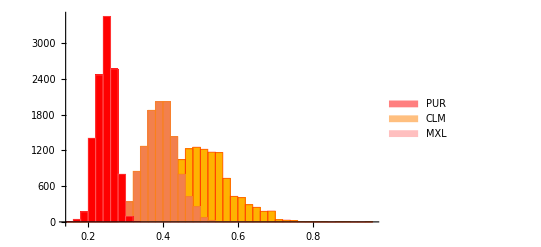

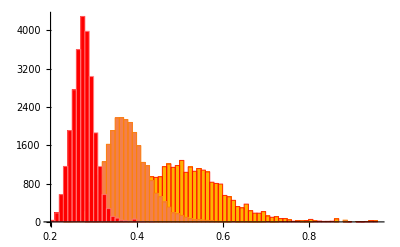
-Graphics--Graphics- | PUR
-Graphics- | CLM
-Graphics- | MXL

```mathematica
Histogram[{Style[ci2sig*Pick[σPUR,selectPUR],{Opacity[1],RGBColor[1,.7,0]}],Style[ ci2sig*Pick[σCLM,selectCLM],{Opacity[1],RGBColor[.95,.5,.3]}],Style[ci2sig*Pick[σMXL,selectMXL],{Opacity[1],Red}]},50,ChartLegends->{"PUR","CLM","MXL"},ChartStyle->{Red,Orange,Pink}]
```

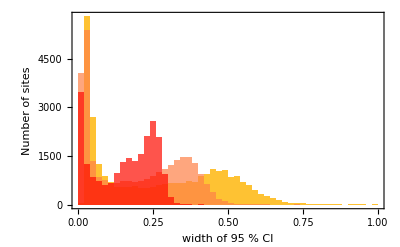

```mathematica
σPURnz=Select[σPUR,#≠0&];
σMXLnz=Select[σMXL,#≠0&];
σCLMnz=Select[σCLM,#≠0&];

figCI=Histogram[{Style[ci2sig*σPURnz/."NA"->0,{Opacity[.8],RGBColor[255/256,.7,0/256],EdgeForm[None]}],Style[ ci2sig*σCLMnz/."NA"->0,{Opacity[.7],RGBColor[255/256,130/256,71/256],EdgeForm[None]}],Style[ci2sig*σMXLnz/."NA"->0,{Opacity[.7],RGBColor[255/256,12/256,0/256],EdgeForm[None]}]},50,Frame->{True,True,False,False},FrameLabel->{"width of 95 % CI", "Number of sites" },LabelStyle->{Larger,FontFamily->"Arial"}]
```

```mathematica
ci2sig
```

3.92

./CI.eps

./CI.pdf

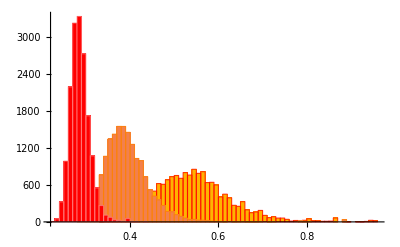
-Graphics--Graphics- | PUR
-Graphics- | CLM
-Graphics- | MXL

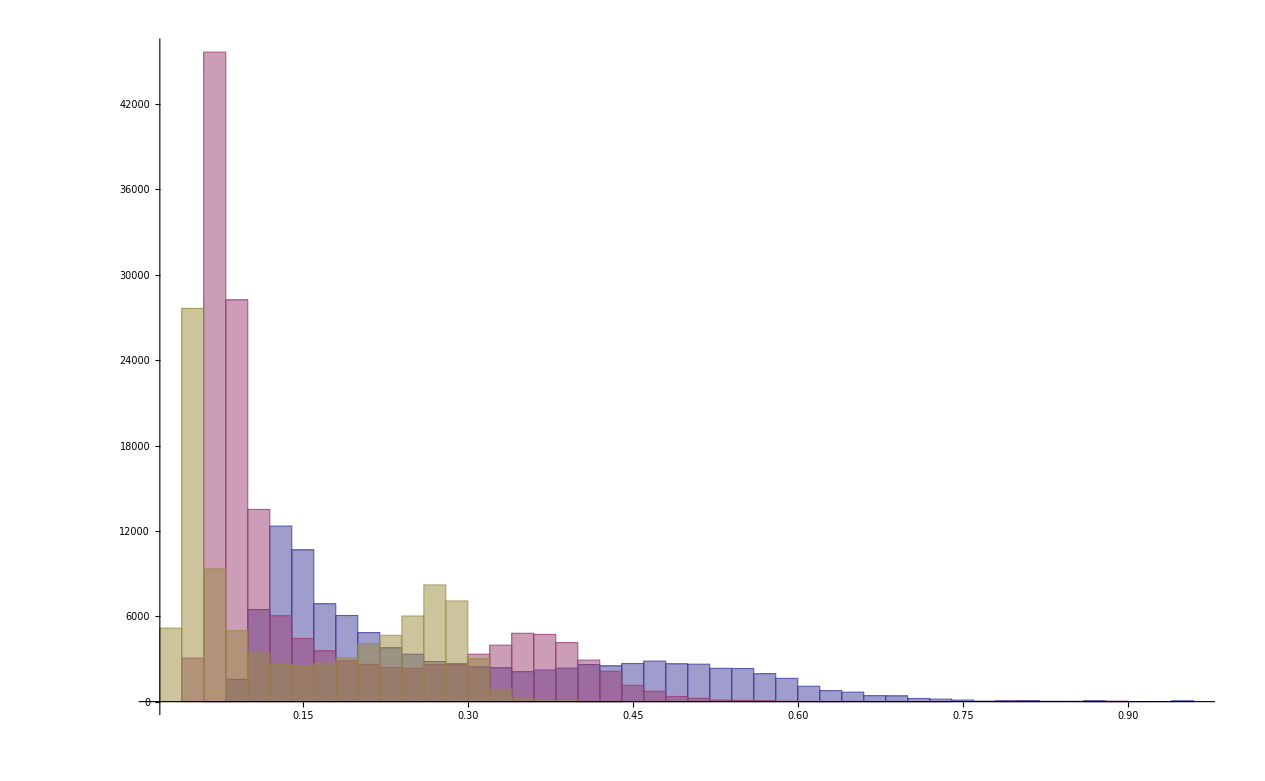
-Graphics--Graphics- | PUR
-Graphics- | CLM
-Graphics- | MXL

```mathematica
Export["./CI.eps",figCI]
Export["./CI.pdf",figCI]
```

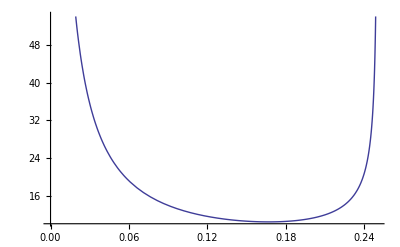

```mathematica
Plot[1/x /Sqrt[1-4x],{x,0,0.25}]
```

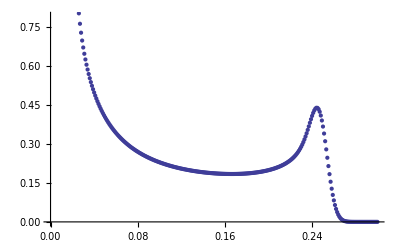

```mathematica
wfun[w_,f_]:=(x (1-x))
ListPlot[Table[{w,NIntegrate[1/f E^(-10000(w-f (1-f))^2),{f,0.00000001,1}]},{w,0,.3,.001}]]
```

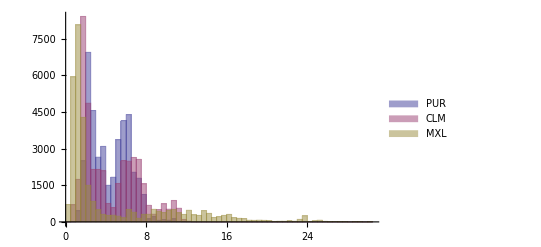

```mathematica
Histogram[{4*Select[σPUR/(xPUR(1-xPUR)),#>0&], 4*Select[σCLM/(xCLM(1-xCLM)),#>0&],4*Select[σMXL/(xMXL(1-xCLM)),#>0&]},50,ChartLegends->{"PUR","CLM","MXL"}]
```

```mathematica
complabel={"CLM vs MXL","CLM vs PUR","PUR vs MXL"}
pseudovariance=0.0
z1=(xCLM-xMXL)/Sqrt[σMXL^2+σCLM^2+pseudovariance];
z2=(xCLM-xPUR)/Sqrt[σPUR^2+σCLM^2+pseudovariance];
z3=(xPUR-xMXL)/Sqrt[σMXL^2+σPUR^2+pseudovariance];

d1=(xCLM-xMXL);
d2=(xCLM-xPUR);
d3=(xPUR-xMXL);
```

{CLM vs MXL,CLM vs PUR,PUR vs MXL}

0.

```mathematica
Mean[d1/."NA"->0]
Mean[d2/."NA"->0]
Mean[d3/."NA"->0]
```

0.00173936

0.00133075

0.000408609

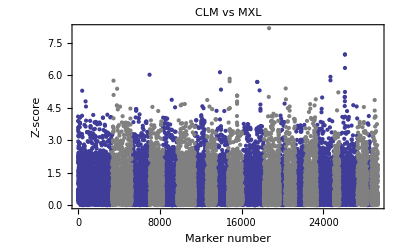

```mathematica
odd=ListPlot[Transpose[{Pick[markerPos,Map[OddQ[#]&,chr]],Pick[Abs[z1],Map[OddQ[#]&,chr]]}],PlotRange->All,Frame->{True,True,False,False} ,FrameLabel->{"Marker number","Z-score"},FrameStyle->Larger];
even=ListPlot[Transpose[{Pick[markerPos,Map[EvenQ[#]&,chr]],Pick[Abs[z1],Map[EvenQ[#]&,chr]]}],PlotStyle->Gray, AxesLabel->{"Marker number","Z-score"}];
Show[odd,even,PlotLabel->complabel[[1]]]
```

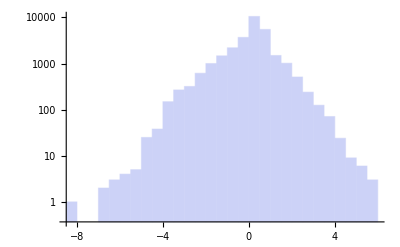

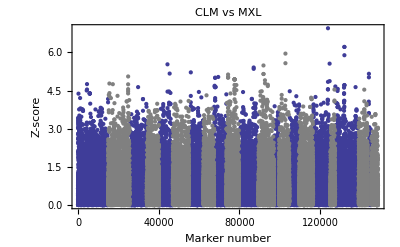

```mathematica
Histogram[z1,30,"LogCount"]
```

```mathematica
postop2=Ordering[Abs[z1],-2]
top2=a⟦postop2⟧
```

{26120,18699}

{{19,17337882,0.,0.032414,0.2,0.46,0.588728,0.71,0.01,0.215002,0.47},{12,47170764,0.,0.010937,0.12,0.38,0.486892,0.58,0.02,0.275554,0.49}}

```mathematica
(*From Z-score to P-value*)
Needs["HypothesisTesting`"]
 pval[x_]:=2*NormalPValue[x]⟦2⟧
```

```mathematica
ps=Map[pval,z1];
n=Length[ps];
unif=Table[i/n,{i,1,n}];
ListPlot[{Transpose[{-Log[unif],-Log[Sort[ps]]}],Transpose[{-Log[unif],-Log[unif]}]},PlotRange->All,Joined->{False,True}]
```

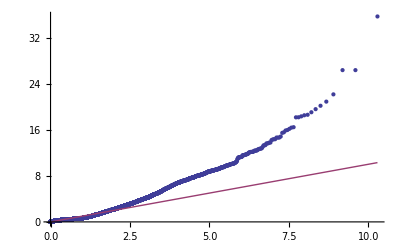

```mathematica
(*z1*)
```

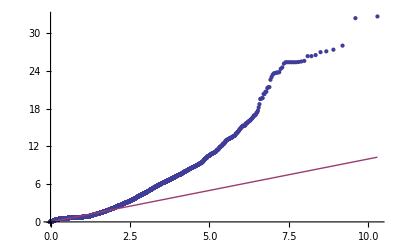

-Graphics-

```mathematica
(*z3*)
```

```mathematica
a[[18699]]
```

{12,47170764,0.,0.010937,0.12,0.38,0.486892,0.58,0.02,0.275554,0.49}

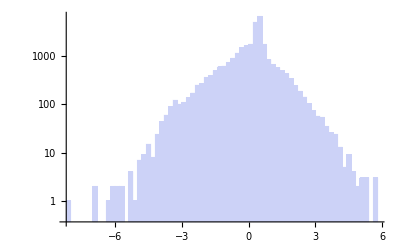

```mathematica
Histogram[z1,50,"LogCount"]
```

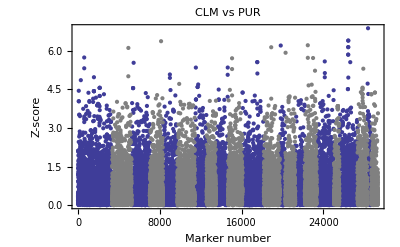

```mathematica
odd=ListPlot[Transpose[{Pick[markerPos,Map[OddQ[#]&,chr]],Pick[Abs[z2],Map[OddQ[#]&,chr]]}],PlotRange->All,Frame->{True,True,False,False} ,FrameLabel->{"Marker number","Z-score"},FrameStyle->Larger];
even=ListPlot[Transpose[{Pick[markerPos,Map[EvenQ[#]&,chr]],Pick[Abs[z2],Map[EvenQ[#]&,chr]]}],PlotStyle->Gray,PlotRange->All];
Show[odd,even,PlotLabel->complabel[[2]]]
```

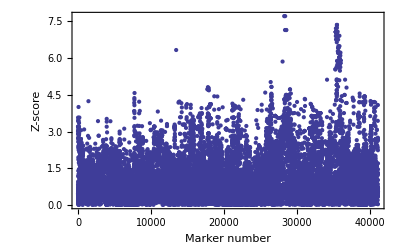

```mathematica
odd
```

```mathematica
mn=Min[z2/."NA"->0]
sel=Map[((#/."NA"->0)==mn)&,z2];
```

-6.77434

```mathematica
Pick[a[[2;;]],sel]
Pick[z1,sel]
Pick[z2,sel]
Pick[z3,sel]
```

{{7,44185088,0,0.0957708,0.32,0.17,0.298073,0.44,0.65,0.886514,0.99}}

{-1.93272}

{-6.77434}

{5.42135}

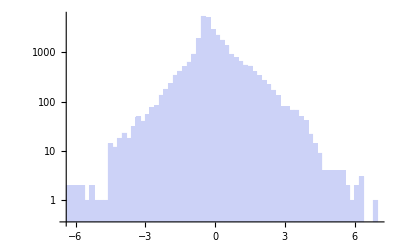

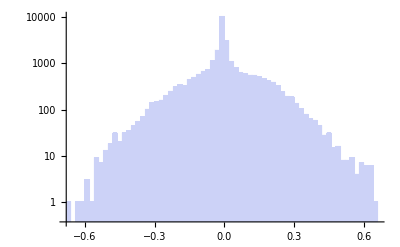

```mathematica
Histogram[z2,50,"LogCount"]
```

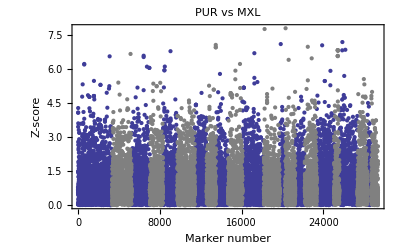

```mathematica
odd=ListPlot[Transpose[{Pick[markerPos,Map[OddQ[#]&,chr]],Pick[Abs[z3],Map[OddQ[#]&,chr]]}],PlotRange->All,Frame->{True,True,False,False} ,FrameLabel->{"Marker number","Z-score"},FrameStyle->Larger];
even=ListPlot[Transpose[{Pick[markerPos,Map[EvenQ[#]&,chr]],Pick[Abs[z3],Map[EvenQ[#]&,chr]]}],PlotStyle->Gray,PlotRange->All];
Show[odd,even,PlotLabel->complabel[[3]]]
```

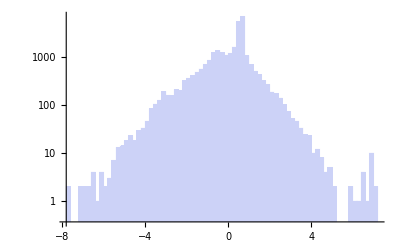

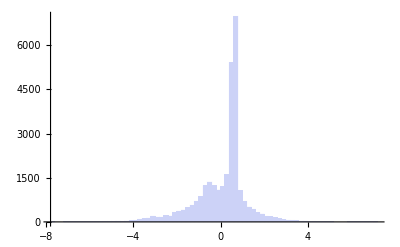

```mathematica
Histogram[z3,50,"LogCount"]
Histogram[z3,50]
```

```mathematica
posedar=Position[a⟦1;;,2⟧,109513601]⟦1,1⟧
Select[a,#⟦2⟧==109513601&]
```

4164

{{2,109513601,0.89,0.965776,0.99,0.95,0.980207,0.99,0.55,0.722026,0.87}}

```mathematica
columns
(*Looking at Edar*)

(*posedar=19280*)
σPUR⟦posedar⟧

a⟦posedar⟧
z1⟦posedar⟧
z2⟦posedar⟧
z3⟦posedar⟧
```

columns

0.1075

{2,109513601,0.89,0.965776,0.99,0.95,0.980207,0.99,0.55,0.722026,0.87}

-0.255021

2.30459

-2.39942

```mathematica
Needs["Combinatorica`"]
N[BinarySearch[Sort[z2/."NA"->0],z2⟦posedar⟧]/Length[z2]]
N[BinarySearch[Sort[d2/."NA"->0],d2⟦posedar⟧]/Length[z2]]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

0.970701

0.963547

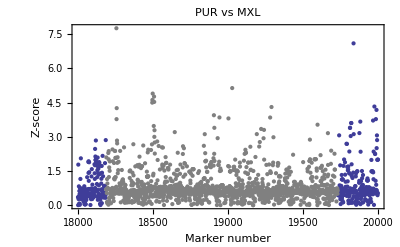

```mathematica
odd=ListPlot[Transpose[{Pick[markerPos⟦18000;;20000⟧,Map[OddQ[#]&,chr⟦18000;;20000⟧]],Pick[Abs[z3]⟦18000;;20000⟧,Map[OddQ[#]&,chr⟦18000;;20000⟧]]}],PlotRange->All,Frame->{True,True,False,False} ,FrameLabel->{"Marker number","Z-score"},FrameStyle->Larger];
even=ListPlot[Transpose[{Pick[markerPos⟦18000;;20000⟧,Map[EvenQ[#]&,chr⟦18000;;20000⟧]],Pick[Abs[z3]⟦18000;;20000⟧,Map[EvenQ[#]&,chr⟦18000;;20000⟧]]}],PlotStyle->Gray,PlotRange->All];
Show[odd,even,PlotLabel->complabel[[3]]]
```

```mathematica
{{markerPos[[posedar]],z3[[posedar]]}}
```

{{4164,-2.39942}}

5200

10200

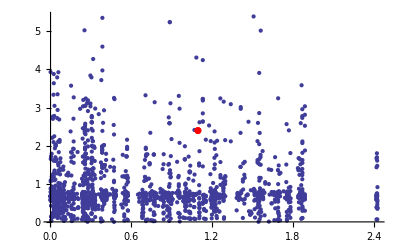

```mathematica
min=5200
max=10200
plot=ListPlot[ Transpose[{Pick[Abs[pos]⟦min;;max⟧,Map[EvenQ[#]&,chr⟦min;;max⟧]],Pick[Abs[z3]⟦min;;max⟧,Map[EvenQ[#]&,chr⟦min;;max⟧]]}],PlotRange->All];
edar=ListPlot[{{pos[[posedar]],Abs[z3[[posedar]]]}},PlotStyle->Red ,PlotMarkers->Automatic];
Show[plot,edar]
```

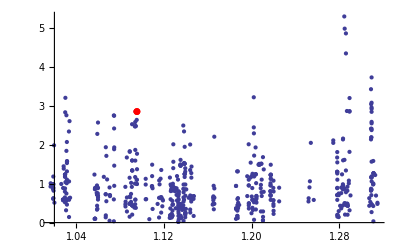

```mathematica
(*1k markers*)
```

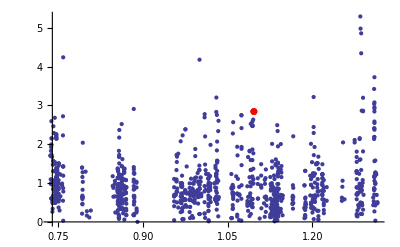

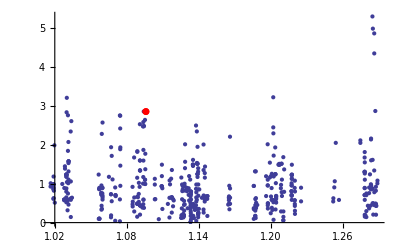

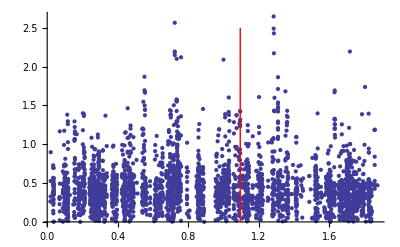

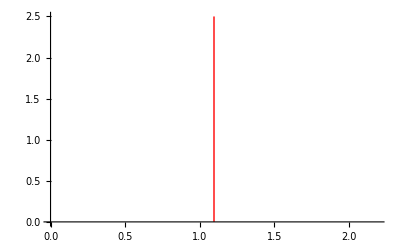

```mathematica
(*2k Markers*)
```

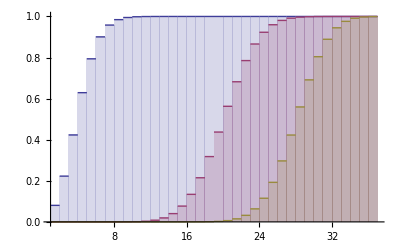

```mathematica
DiscretePlot[Evaluate@Table[CDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}],{k,36},ExtentSize->Right]
```

```mathematica
(*given a mean value and 95% confidence interval, we wish to recover a Binomial distribution sample size N and sampling event n that will yield the same mean and CI width*)
ci2contingency[mean_,low_,high_]:=1
```

```mathematica
InverseCDF[BinomialDistribution[40,.1],.8]
```

6

```mathematica
invsmooth[NN_,p_,c_]:=Module[{a,v,v1}, 
a=InverseCDF[BinomialDistribution[NN,p],c];
If[a==0,Return[0]];
v=CDF[BinomialDistribution[NN,p],a];
v1=CDF[BinomialDistribution[NN,p],a-1];
a-1+(c-v1)/(v-v1)
];

invsmooth[NN_,p_,c_]:=Module[{a,v,v1},
 
a=InverseCDF[BinomialDistribution[NN,p],c];
If[a==0,Return[ ((1-CDF[BinomialDistribution[NN,p],0])/(1-c)) ]];
v=CDF[BinomialDistribution[NN,p],a];
v1=CDF[BinomialDistribution[NN,p],a-1];
(a+((c-v1)/(v-v1))^1.5)
];
(*A smoothed inverse CDF. There is an interpolation between nearest integers (the power of 1.5 was chosen by hand to obtain a function with apparently smooth derivatives)
The interpolation for a=0 is proportional to the proportion if the distribution beyond 0 to that c. So if c is 0.95, and 0.975 of the data is in bin 0, we get a inv of 0.5. This is done to ensure that the inv function is monotonous.    *)




width[NN_,p_]:=Mean[Table[(InverseCDF[BinomialDistribution[NN,p],.975+i]-InverseCDF[BinomialDistribution[NN,p],.025+i])/NN,{i,-0.02,0.02,.02}]] 
widths[NN_,p_]:=(invsmooth[NN,p,.975]-invsmooth[NN,p,.025])/NN (*Averaging over offsets to smooth out integer boundary effects *)
```

```mathematica
CDF[BinomialDistribution[10,.1],3]
InverseCDF[BinomialDistribution[10,.1],.9872]
invsmooth[10,.1,.9873]
```

0.987205

3

3.00853

```mathematica
vecTopCLM=top2⟦2⟧⟦3;;5⟧
NtopCLM=f2[vecTopCLM]
vecTopMXL=top2⟦2⟧⟦6;;8⟧
NtopMXL=f2[vecTopMXL]
```

{0.,0.010937,0.12}

12

{0.38,0.486892,0.58}

108

12

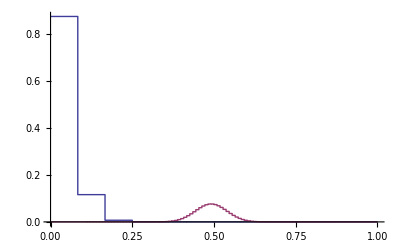

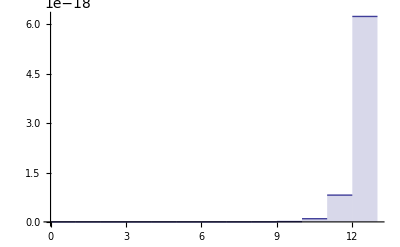

```mathematica
(*Plot the fitted Binomial distributions to eac, to have a look at whethr they make sense.*)
ListPlot[{Table[{i/NtopCLM, PDF[BinomialDistribution[NtopCLM,vecTopCLM⟦2⟧],i]},{i,0,12}],Table[{i/NtopMXL, PDF[BinomialDistribution[NtopMXL,vecTopMXL⟦2⟧],i]},{i,0,NtopMXL}]},PlotRange->All,Joined->True,InterpolationOrder->0]
DiscretePlot[PDF[BinomialDistribution[NtopMXL,vecTopMXL⟦2⟧],i]/NtopCLM,{i,0,12},PlotRange->All,ExtentSize->Right]
```

```mathematica
nboot=3*10^7;
BootCLM=RandomVariate[BinomialDistribution[NtopCLM,vecTopCLM⟦2⟧],nboot]/NtopCLM;
BootMXL=RandomVariate[BinomialDistribution[NtopMXL,vecTopMXL⟦2⟧],nboot]/NtopMXL;
Length[Select[BootCLM-BootMXL,#>0&]]
```

1

```mathematica
Length[a]
1./nboot * Length[a]
```

29354

0.000978467

0

```mathematica
meanpos=2;
maxpos=3;
minpos=1;
f[vec_]:=NMinimize[{(width[NN,vec⟦meanpos⟧]-(vec⟦maxpos⟧-vec⟦minpos⟧))^2,NN∈Integers,NN>0},{NN}][[2,1,2]]

f2[vec_]:=If[vec⟦maxpos⟧<10^(-8),120(*This is a hack because reounding inaccuracy in the EM code *),
   Ordering[Table[(width[NN,vec⟦meanpos⟧]-(vec⟦maxpos⟧-vec⟦minpos⟧))^2,{NN,1,120,4}],1]⟦1⟧*4]
```

```mathematica
Timing[Map[f,a⟦1;;30,3;;5⟧]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

$Aborted

```mathematica
neffCLM= ParallelMap[f2,a⟦1;;300,3;;5⟧];
neffMXL= ParallelMap[f2,a⟦1;;300,6;;8⟧];
neffPUR=ParallelMap[f2,a⟦1;;300,9;;11⟧];
```

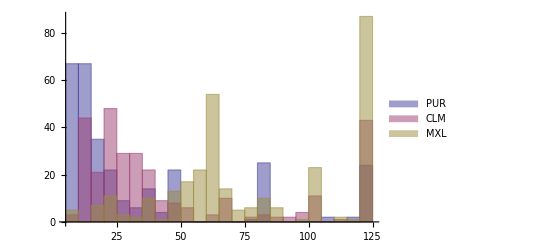

```mathematica
Histogram[{neffPUR,neffCLM,neffMXL},20,ChartLegends->{"PUR","CLM","MXL"}]
```

```mathematica
(*Why does MXL have "4"s when the other ones don't?*)
neffMXL[[1;;100]]
neffPUR[[1;;100]]
```

```mathematica
a[[3]]
```

{1,979748,0.,0.001514,0.01,0.,0.000215,0.,0.,0.003531,0.02}

```mathematica
mx
```

0.00043

```mathematica
f2[{0,.5,0}]
```

120

```mathematica
vec=a[[3,6;;8]]
```

{0.,0.000215,0.}

```mathematica
widths[10,0.001]
```

0.0959552

```mathematica
invsmooth[10,.003,.975]
invsmooth[10,0.003,.025]
InverseCDF[BinomialDistribution[10,0.001],0.975]
CDF[BinomialDistribution[10,0.001],0]
```

1.06249

0.0303572

0

0.990045

{28.35179,{6,7,7,13,6,2,8,8,3,4,5,2,7,5,3,8,8,9,4,1,1,13,16,4,10,2,1,2,7,11}}

```mathematica
width[5,vec⟦meanpos⟧]
```

3/7

```mathematica
vec=a[[2,3;;5]]
```

{0.85,0.962622,0.99}

```mathematica
f[vec]
```

6

0.

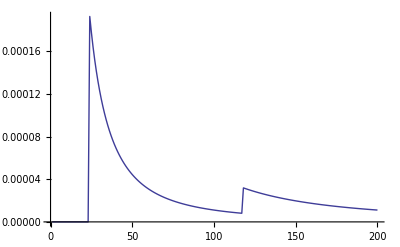

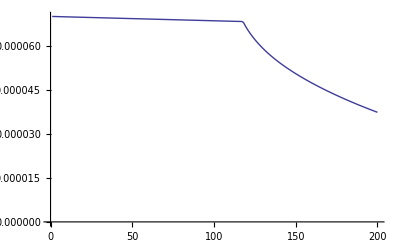

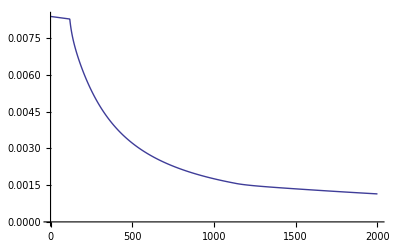

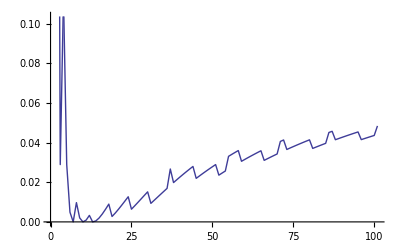

```mathematica
(vec⟦maxpos⟧-vec⟦minpos⟧)
ListPlot[Table[(width[NN,vec⟦meanpos⟧]-(vec⟦maxpos⟧-vec⟦minpos⟧))^2,{NN,1,200}],Joined->True,PlotRange->{0.,All}]
ListPlot[Table[(widths[NN,vec⟦meanpos⟧]-(vec⟦maxpos⟧-vec⟦minpos⟧))^2,{NN,1,200}],Joined->True,PlotRange->{0.,All}]
ListPlot[Table[widths[NN,vec⟦meanpos⟧],{NN,1,2000}],Joined->True,PlotRange->{0.,All}]
```

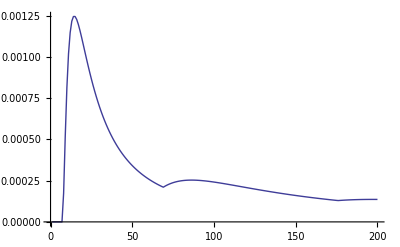

```mathematica
ListPlot[Table[(widths[NN,vec⟦meanpos⟧])^2,{NN,1,200}],Joined->True,PlotRange->{0.,All}]
```

0.01

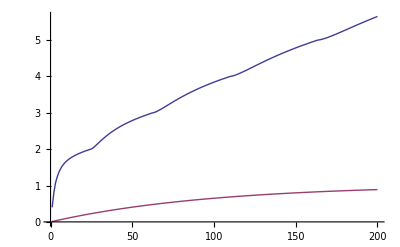

```mathematica
vec⟦meanpos⟧=0.01
ListPlot[{Table[invsmooth[NN,vec⟦meanpos⟧,.975],{NN,1,200}],Table[invsmooth[NN,vec⟦meanpos⟧,.025],{NN,1,200}]},Joined->True]
```